## Atomic to Physical Unit Conversions

```mathematica
(* Converting Atomic Units into Lab Units *)
Module[{enAU,enAU1GHz,tAU,tAU1ns,fAU,fAU1mVcm},
(* 1 GHz below ZFIP in AU *)
enAU=Quantity[4.35974417*10^-18,"Joules"];
enAU1GHz=UnitConvert[Quantity["PlanckConstant"]*Quantity[1,"Gigahertz"]/enAU];
Print["1 GHz Photon Energy = ",enAU1GHz, " A.U."];

(* 1 ns in AU *)
tAU=Quantity[2.418884326505*10^-17,"Seconds"];
tAU1ns=UnitConvert[Quantity[1,"nanosecond"]/tAU];
Print["1 ns = ",tAU1ns, " A.U."];

(* 1 mV/cm in AU *)
fAU=Quantity[5.14220652*10^11,"Volts"/"Meters"];
fAU1mVcm=UnitConvert[Quantity[1,"Millivolts"/"Centimeters"]/fAU];
Print["1 mV/cm = ",fAU1mVcm," A.U."];

(* Association *)
au=Association[{"GHz"->enAU1GHz,"ns"->tAU1ns,"mVcm"->fAU1mVcm}]
];
```

1 GHz Photon Energy = 1.51983×10^-7 A.U.

1 ns = 4.13414×10^7 A.U.

1 mV/cm = 1.94469×10^-13 A.U.

```mathematica
au["GHz"]
au["ns"]
au["mVcm"]
```

1.51983×10^-7

4.13414×10^7

1.94469×10^-13

## Solver and Helper Functions

```mathematica
solver=Function[
{ic,fields,timing}, (* ic, fields, timing *)
(* A solver based only on initial conditions,physical conditions and start and stop times. *)
ClearAll[x,z,t];
(* Unpack *)
{x0,z0,vx0,vz0}=ic;
{fpulse,fmw,ω,α}=fields;
{toff,τring,t0,tmax}=timing;
(* solve *)
sol=NDSolve[
{
x''[t]==-x[t]/(x[t]^2+z[t]^2)^(3/2), (* -r/r^3 *)
x'[t0]==vx0,
x[t0]==x0,
z''[t]==-z[t]/(x[t]^2+z[t]^2)^(3/2) (* -r/r^3 *)
-fpulse*If[t<toff,1,0] (* Field that switches off *)
-fmw*Sin[ω*t+α]*If[t<toff,1,E^(-(t-toff)/τring)], (* MW that rings down *)
z'[t0]==vz0,
z[t0]==z0
},
{x,z},{t,t0,tmax},AccuracyGoal->13,PrecisionGoal->13,MaxSteps->1000000
];
(* return *)
sol];
```

```mathematica
icstarting=Function[
{w0,l0,θLRL,dL},
(* For starting the simulation with known energy, angular momentum, orientation, and angular momentum direction *)
(* r0 and v0 from initial energy *)
If[w0==0,
r0=l0^2/2;
v0=2/l0;
,
r0=(-1+√(1+2*w0*l0^2))/(2*w0);
v0=(1+√(1+2*w0*l0^2))/l0;
];
(* Orient r and v based on θLRL and dL *)
x0=r0*Sin[θLRL];
z0=-r0*Cos[θLRL];
vx0=dL*v0*Cos[θLRL];
vz0=dL*v0*Sin[θLRL];
{x0,z0,vx0,vz0}];
```

## Evaluation Functions

```mathematica
wfunc=Function[{x,z,vx,vz},
1/2*(vx^2+vz^2)-1/√(x^2+z^2)];
rfunc=Function[{x,z},
√(x^2+z^2)];
lfunc=Function[{x,z,vx,vz},
z*vx-x*vz];
wslingshot=Function[
{t,fmw,ω},
-√3*3/2*fmw/ω^(2/3)*Cos[ω*t+α]
];
```

```mathematica
wslingshot[0.5*au["ns"],fmw,ω]
```

-2.33335×10^-6

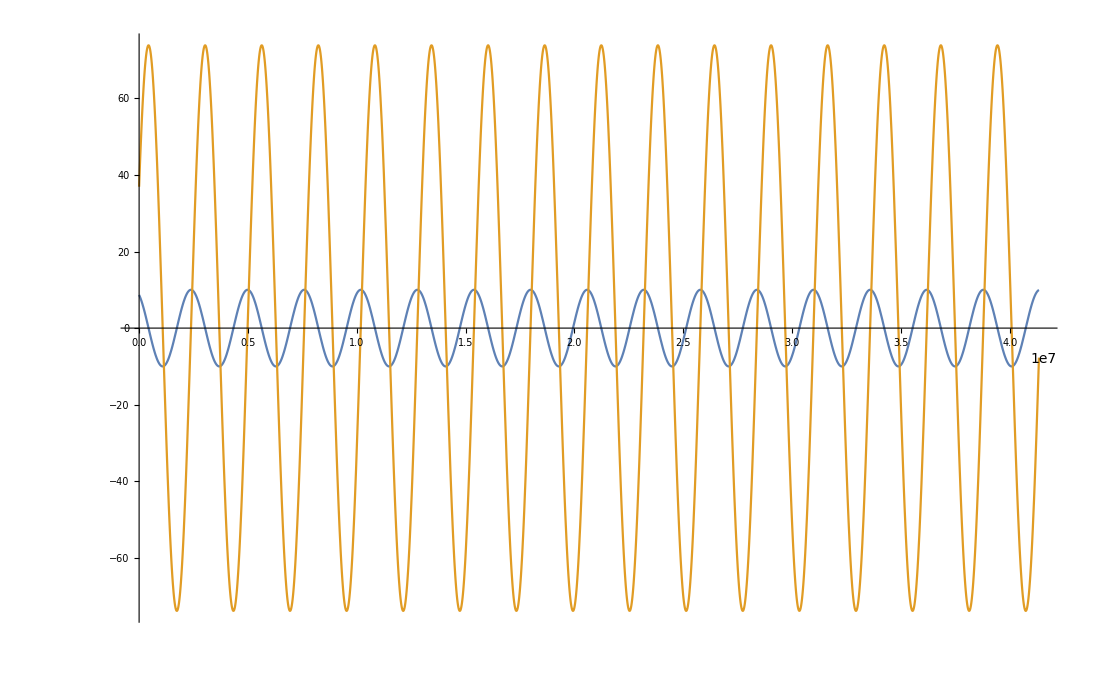

```mathematica
Plot[{10*Sin[ω*t+α],wslingshot[t,fmw,ω]/au["GHz"]},{t,0,1*au["ns"]}]
```

## Settings

```mathematica
(* IC *)
w0=-28*au["GHz"];
l0=√(3*(3+1));
θLRL=0;
dL=1;
(* Field parameters *)
fpulse=0*0.72*au["mVcm"];
fmw=4*1000*au["mVcm"];
ω=2*π*15.9/au["ns"];
α=4π/6;
(* timing *)
toff=20*au["ns"];
τring=10*au["ns"];
t0=0;
tmax=toff+5*τring;
(* Getting ic for the solver *)
{x0,z0,vx0,vz0}=icstarting[w0,l0,θLRL,dL];
(* Packaging *)
ic={x0,z0,vx0,vz0};
fields={fpulse,fmw,ω,α};
timing={toff,τring,t0,tmax};
```

## Execution

```mathematica
soldata=EvaluationData[solver[ic,fields,timing]];
```

```mathematica
sol=soldata["Result"][[1]];
tlims=sol[[1,2]]["Domain"][[1]];
ts=FindMinimum[rfunc[x[t],z[t]]/.sol,{t,5.95*au["ns"]}][[2,1,2]];
qr=QuotientRemainder[ts*ω+α+π/2,π]; (* Q is # of periods, R is radians away from ϕ=0 *)
tminus=ts-(2π+qr[[2]])/ω;
tplus=ts+(2π+(π-qr[[2]]))/ω;
style={Red,Thick};
wplus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tplus];
wminus=wfunc[x[t],z[t],x'[t],z'[t]]/.Append[sol,t->tminus];
gridlines={{{ts/au["ns"],style},{ts/au["ns"]-2π/(ω*au["ns"]),style},{tminus/au["ns"],style},{ts/au["ns"]+2π/(ω*au["ns"]),style},{tplus/au["ns"],style}},{{wplus/au["GHz"],style},{wminus/au["GHz"],style}}};
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
wslingshot[ts,fmw,ω]/au["GHz"]
```

23.3246

```mathematica
wplusave=ω/(10*2*π)*NIntegrate[wfunc[x[t],z[t],x'[t],z'[t]]/.sol,{t,tplus,tplus+10*2π/ω}];
wminusave=ω/(10*2*π)*NIntegrate[wfunc[x[t],z[t],x'[t],z'[t]]/.sol,{t,tminus-10*2π/ω,tminus}];
```

```mathematica
(wplusave-wminusave)/au["GHz"]
```

23.4827

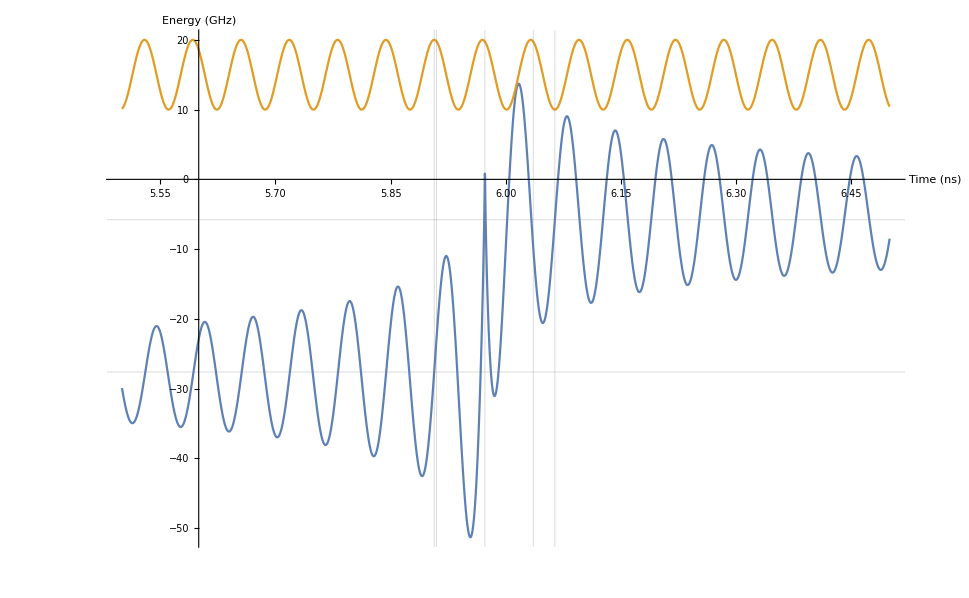

```mathematica
Plot[{(wfunc[x[ta],z[ta],x'[ta],z'[ta]]/.Append[sol,ta->(t*au["ns"])])/au["GHz"],(5*Sin[ω*ta+α]+15)/.ta->(t*au["ns"])}
,{t,5.5,6.5},GridLines->gridlines,AxesLabel->{"Time (ns)","Energy (GHz)"}]
(* Plot[rfunc[x[ta],z[ta]]/.Append[sol,ta->(t*au["ns"])],{t,5.5,6.5},AxesLabel->{"Time (ns)","Radius (a.u.)"}] *)
```

```mathematica
rfunc[x[ta],z[ta]]/.Append[sol[[1]],ta->tlims[[2]]]
```

0.00802156

```mathematica
mint=FindMinimum[rfunc[x[t],z[t]]/.sol[[1]],{t,1.7*au["ns"]}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
mint[[2,1,2]]
```

6.91715×10^7

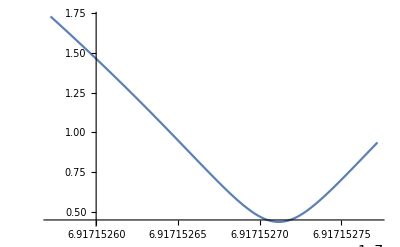

```mathematica
Plot[rfunc[x[t],z[t]]/.sol,{t,mint[[2,1,2]]-1,mint[[2,1,2]]+1}]
```